```mathematica
(* Lab 2 - Ex 4,7 *)
```

```mathematica
(* Ex 4 *)
```

```mathematica
f[x_]:=x^3-6*x^2+11*x-6.1
```

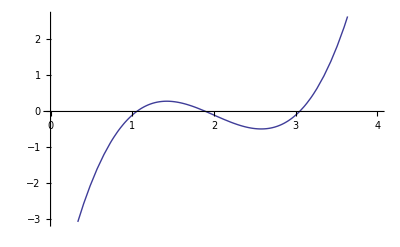

```mathematica
Plot[f[x],{x,0,4}]
```

```mathematica
(* Newton-Rophson *)
```

```mathematica
NewRoph[i_] :=Module[{iterations=i},
y0=3.5;
For[index=0, index<iterations,
y1=y0-f[y0]/f'[y0]; y0=y1;index++];
y0
]
```

```mathematica
NewRoph[3]
```

3.04732

```mathematica
(* Secant *)
```

```mathematica
secant[i_] :=Module[{iterations=i},
y0=2.5;
y1=3.5;
For[index=0, index<iterations,
y2=y1-(f[y1]*(y0-y1))/(f[y0]-f[y1]); index++;
 y0=y1;y1=y2];
y1
]
```

```mathematica
secant[3]
```

3.22192

```mathematica
(* Modified secant *)
```

```mathematica
modsecant[i_] :=Module[{iterations=i},
y0=3.5;
delta=0.01;
For[index=0, index<iterations,
y1=y0-(f[y0]*delta)/(f[y0+delta]-f[y0]); index++;
 y0=y1];
y0
]
```

```mathematica
modsecant[3]
```

3.04774

```mathematica
Roots[f[x]==0,x]
```

x==1.05435||x==1.89897||x==3.04668

```mathematica
(* Ex 7 *)
(* function definitions *)
```

```mathematica
pCO[t_]:=0.012226(t-1983)^2+1.418542(t-1983)+342.38309
```

```mathematica
pH[H_]:=-Log10[H]
```

```mathematica
KH=10^(-1.46)
```

0.0346737

```mathematica
K1[H_,HCO_,pCO_]:=10^6*(H*HCO)/(KH*pCO)
```

```mathematica
K2[H_,CO_,HCO_]:=(H*CO)/HCO
```

```mathematica
Kw[H_,OH_]:=H*OH
```

```mathematica
cT[pCO_,HCO_,CO_]:=(KH*pCO)/10^6+HCO+CO
```

```mathematica
f[HCO_,CO_,OH_,H_]:=HCO+2*CO+OH-H
```

```mathematica
pCO1958=315
pCO2008=386
```

315

386

```mathematica
(* real solution computation*)
```

```mathematica
sols=NSolve[{K1[H,HCO,pCO1958]==10^(-6.3),K2[H,CO,HCO]==10^(-10.3),Kw[H,OH]==10^(-14),f[HCO,CO,OH,H]==0},{H,HCO,CO,OH}]
```

{{H→0.,HCO→-0.0547108,CO→0.0274054,OH→-0.0000999454},{H→2.34186×10^-6,HCO→2.33749×10^-6,CO→5.00252×10^-11,OH→4.27011×10^-9},{H→-2.34176×10^-6,HCO→-2.33759×10^-6,CO→5.00295×10^-11,OH→-4.27029×10^-9}}

```mathematica
{h1,hco1,co1,oh1}={H,HCO,CO,OH}/. sols[[2]]
```

{2.34186×10^-6,2.33749×10^-6,5.00252×10^-11,4.27011×10^-9}

```mathematica
ct=cT[pCO1958,hco1,co1]
```

0.0000132598

```mathematica
(* solution for 1958 *)
```

```mathematica
pH[h1]
```

5.63044

```mathematica
sols=NSolve[{K1[H,HCO,pCO2008]==10^(-6.3),K2[H,CO,HCO]==10^(-10.3),Kw[H,OH]==10^(-14),f[HCO,CO,OH,H]==0},{H,HCO,CO,OH}]
```

{{H→0.,HCO→-0.06702,CO→0.0335599,OH→-0.0000999118},{H→2.59194×10^-6,HCO→2.58799×10^-6,CO→5.00422×10^-11,OH→3.85811×10^-9},{H→-2.59184×10^-6,HCO→-2.58809×10^-6,CO→5.00461×10^-11,OH→-3.85826×10^-9}}

```mathematica
{h2,hco2,co2,oh2}={H,HCO,CO,OH}/. sols[[2]]
```

{2.59194×10^-6,2.58799×10^-6,5.00422×10^-11,3.85811×10^-9}

```mathematica
ct=cT[pCO2008,hco2,co2]
```

0.0000159721

```mathematica
(* solution for 2008 *)
```

```mathematica
pH[h2]
```

5.58637

```mathematica
(* rewrite equations as a single one, depending solely on H *)
```

```mathematica
f1[k1_,k2_,kw_,pCO_]:=k1/(10^6*H)*KH*pCO+2*(k2*k1)/(10^6*H^2)*KH*pCO+kw/H-H
```

```mathematica
eq1[H_]=f1[10^(-6.3),10^(-10.3),10^(-14),pCO1958]
```

(5.48707×10^-22)/H^2+(5.48407×10^-12)/H-H

```mathematica
eq2[H_]=f1[10^(-6.3),10^(-10.3),10^(-14),pCO2008]
```

(6.72384×10^-22)/H^2+(6.71791×10^-12)/H-H

```mathematica
(* Solution using Bisection for 1958 *)
```

```mathematica
bisection1958[l_,u_]:=Module[{xl=l,xu=u,xr=(l+u)/2,er=100},
aproxErr={};
trueErr={};
xrs={};
While[er>0.01,If[eq1[xr]*eq1[xu]<0,xl=xr,xu=xr];er=Abs[(((xl+xu)/2)-xr)/(xl+xu)/2]*100;AppendTo[aproxErr,er//N];AppendTo[trueErr,Abs[(5.630439124537583-pH[xr])/5.630439124537583]*100//N];
AppendTo[xrs,xr//N];
xr=(xl+xu)/2];
{xr//N,xrs,aproxErr,trueErr}
];
```

```mathematica
sol1=bisection1958[H /. Solve[pH[H]==12,H][[1]],H /. Solve[pH[H]==2,H][[1]]]
```

{2.34187×10^-6,{0.005,0.0025,0.00125,0.000625,0.0003125,0.00015625,0.000078125,0.0000390625,0.0000195313,9.76563×10^-6,4.88281×10^-6,2.44141×10^-6,1.2207×10^-6,1.83106×10^-6,2.13623×10^-6,2.28882×10^-6,2.36511×10^-6,2.32697×10^-6,2.34604×10^-6,2.3365×10^-6,2.34127×10^-6,2.34366×10^-6,2.34246×10^-6},{25.,25.,25.,25.,25.,25.,25.,25.,25.,25.,25.,25.,8.33333,3.57143,1.66667,0.806451,0.409836,0.203252,0.102041,0.0509165,0.0254323,0.0127226,0.00636294},{59.1323,53.7858,48.4394,43.0929,37.7464,32.3999,27.0535,21.707,16.3605,11.014,5.66757,0.3211,5.02537,1.89789,0.708871,0.176707,0.0762121,0.0492107,0.0137556,0.0176633,0.0019378,0.00591291,0.00198855}}

```mathematica
pH[sol1[[1]]]
```

5.63044

```mathematica
(* Solution using Bisection for 2008 *)
```

```mathematica
bisection2008[l_,u_]:=Module[{xl=l,xu=u,xr=(l+u)/2,er=100},
aproxErr={};
trueErr={};
xrs={};
While[er>0.01,If[eq2[xr]*eq2[xu]<0,xl=xr,xu=xr];er=Abs[(((xl+xu)/2)-xr)/(xl+xu)/2]*100;AppendTo[aproxErr,er//N];AppendTo[trueErr,Abs[(5.586374485591752-pH[xr])/5.586374485591752]*100//N];
AppendTo[xrs,xr//N];
xr=(xl+xu)/2];
{xr//N,xrs,aproxErr,trueErr}
];
```

```mathematica
sol2=bisection2008[H /. Solve[pH[H]==12,H][[1]],H /. Solve[pH[H]==2,H][[1]]]
```

{2.59221×10^-6,{0.005,0.0025,0.00125,0.000625,0.0003125,0.00015625,0.000078125,0.0000390625,0.0000195313,9.76563×10^-6,4.88281×10^-6,2.44141×10^-6,3.66211×10^-6,3.05176×10^-6,2.74658×10^-6,2.594×10^-6,2.5177×10^-6,2.55585×10^-6,2.57492×10^-6,2.58446×10^-6,2.58923×10^-6,2.59161×10^-6,2.5928×10^-6},{25.,25.,25.,25.,25.,25.,25.,25.,25.,25.,25.,8.33333,5.,2.77778,1.47059,0.757575,0.373134,0.185185,0.0922509,0.0460405,0.0229991,0.0114942,0.00574845},{58.81,53.4213,48.0327,42.644,37.2554,31.8667,26.4781,21.0894,15.7008,10.3121,4.92349,0.465155,2.687,1.2696,0.450511,0.00615146,0.225931,0.109024,0.0512228,0.0224827,0.00815244,0.000997201,0.00257795}}

```mathematica
pH[sol2[[1]]]
```

5.58633